Unit step function

```mathematica
Step1[x_]:=HeavisideTheta[x]-HeavisideTheta[x-1]
```

Graph unit step function

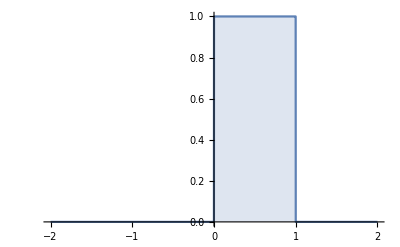

```mathematica
Plot[Step1[x],{x,-2,2}, Filling-> Bottom]
```

Unit step function with prescribed support interval

```mathematica
Step2[x_,a_,b_]:=Step1[(x-a)/(b-a)];
```

Example of graphs

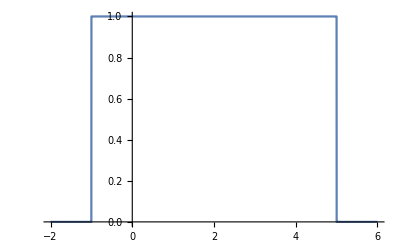

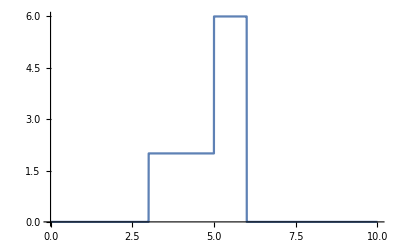

```mathematica
Plot[Step2[x,-1,5],{x,-2,6}]
Plot[2*Step2[x,3,5]+6*Step2[x,5,6],{x,0,10}]
```

Homogeneous partition of  interval [a,b] with length n

```mathematica
HomogeneousP[a_,b_,n_]:=Table[a+(i)*((b-a)/n),{i,0,n}];
```

Example homogeneous partition

```mathematica
HomogeneousP[0,10,10]
```

{0,1,2,3,4,5,6,7,8,9,10}

Choosing sampling point for heights in Riemann sum, given a partition P

```mathematica
LeftPoint[P_]:=Table[P[[i]],{i,1,Length[P]-1}];
RightPoint[P_]:=Table[P[[i+1]],{i,1,Length[P]-1}];
MidPoint[P_]:=Table[(P[[i]]+P[[i+1]])/2,{i,1,Length[P]-1}];
RandomPointSample[P_]:=Table[RandomPoint[Interval[{P[[i]],P[[i+1]]}]],{i,1,Length[P]-1}];
```

Examples of sampling points

```mathematica
P0=HomogeneousP[-2,15,30];
LeftPoint[P0]
RightPoint[P0]
MidPoint[P0]
RandomPointSample[P0]
```

{-2,-43/30,-13/15,-3/10,4/15,5/6,7/5,59/30,38/15,31/10,11/3,127/30,24/5,161/30,89/15,13/2,106/15,229/30,41/5,263/30,28/3,99/10,157/15,331/30,58/5,73/6,191/15,133/10,208/15,433/30}

{-43/30,-13/15,-3/10,4/15,5/6,7/5,59/30,38/15,31/10,11/3,127/30,24/5,161/30,89/15,13/2,106/15,229/30,41/5,263/30,28/3,99/10,157/15,331/30,58/5,73/6,191/15,133/10,208/15,433/30,15}

{-103/60,-23/20,-7/12,-1/60,11/20,67/60,101/60,9/4,169/60,203/60,79/20,271/60,61/12,113/20,373/60,407/60,147/20,95/12,509/60,181/20,577/60,611/60,43/4,679/60,713/60,249/20,781/60,163/12,283/20,883/60}

{{-1.64229},{-0.867202},{-0.475348},{-0.188777},{0.729356},{0.968835},{1.92634},{2.33228},{2.67393},{3.26668},{3.83225},{4.57821},{4.83764},{5.65179},{6.07228},{6.96588},{7.23359},{7.93498},{8.52358},{9.06642},{9.85359},{10.1732},{10.8336},{11.4653},{11.8792},{12.654},{12.88},{13.4365},{14.2139},{14.6823}}

Función escalonada sobre partición homogenea P de longitud n con puntos muestra S dados por f

```mathematica
StepFunction2[f_,P_,S_]:=Sum[f[S[[i]]]Step2[x,P[[i]],P[[i+1]]],{i,1,Length[P]-1}];
```

Ejemplos de funciones escalonadas

```mathematica
f[x_]:=x^2;
```

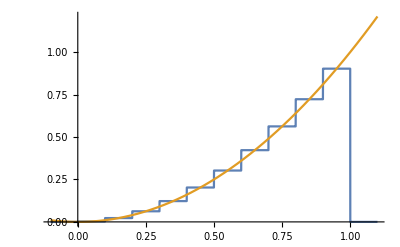

```mathematica
Plot[{StepFunction2[f,HomogeneousP[0,1,10],MidPoint[HomogeneousP[0,1,10]]],f[x]},{x,-0.1,1.1}]
```

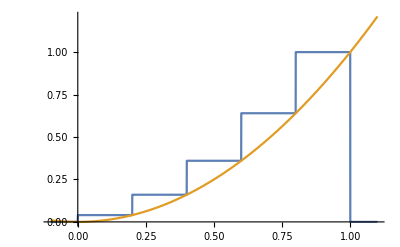

```mathematica
Plot[{StepFunction2[f,HomogeneousP[0,1,5],RightPoint[HomogeneousP[0,1,5]]],f[x]},{x,-0.1,1.1}]
```

```mathematica
HomogeneousP[0,Pi,20]
S=RandomPointSample[HomogeneousP[0,Pi,20]]
```

{0,π/20,π/10,(3 π)/20,π/5,π/4,(3 π)/10,(7 π)/20,(2 π)/5,(9 π)/20,π/2,(11 π)/20,(3 π)/5,(13 π)/20,(7 π)/10,(3 π)/4,(4 π)/5,(17 π)/20,(9 π)/10,(19 π)/20,π}

{{0.153698},{0.229951},{0.460736},{0.623435},{0.762434},{0.897426},{0.962044},{1.23175},{1.36571},{1.48059},{1.64873},{1.85654},{1.93903},{2.08354},{2.3373},{2.37939},{2.63814},{2.69607},{2.9296},{3.11531}}

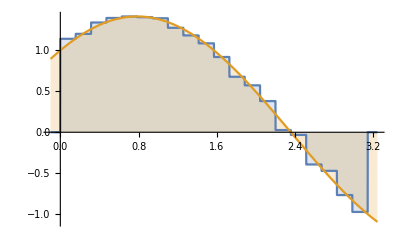

```mathematica
Plot[{StepFunction2[f,HomogeneousP[0,Pi,20],S],f[x]},{x,-0.1,Pi+0.1},Filling->Axis]
```

Problem with random sample, it seems there is a double loop, seprate computation for random sample works

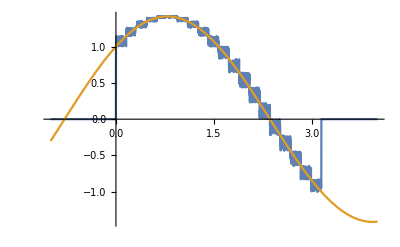

```mathematica
Plot[{StepFunction2[f,HomogeneousP[0,Pi,20],RandomPointSample[HomogeneousP[0,Pi,20]]],f[x]},{x,-1,4}]
```

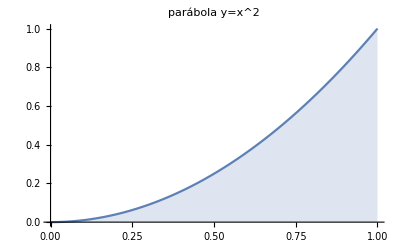

```mathematica
Plot[x^2,{x,0,1},Filling->Axis,PlotLabel->Style["parábola y=x^2",FontSize->15]]
```

```mathematica
f[x_]:=x^2;
line=Line[{1,0},{1,2}]
```

Line[{1,0},{1,2}]

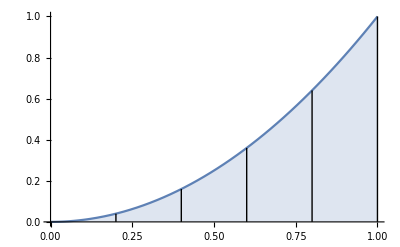

```mathematica
Plot[f[x],{x,0,1}, 
Epilog->
{Line[{{0.2,0},{0.2,(0.2)^2}}],
Line[{{0.4,0},{0.4,(0.4)^2}}],
    Line[{{0.6,0},{0.6,(0.6)^2}}],
Line[{{0.8,0},{0.8,(0.8)^2}}],
Line[{{1,0},{1,1}}]
},Filling->Axis]
```